## General

## Configuration

```mathematica
(*enable assertions*)
On[Assert];
```

## Units

```mathematica
{ns,us,ms}={10^-9,10^-6,10^-3};
```

```mathematica
{khz,mhz,ghz}={10^3,10^6,10^9};
{wkhz,wmhz,wghz}=2π*{10^3,10^6,10^9};
```

```mathematica
{mv,uv}={10^-3,10^-6};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[ListPlot,PlotRange->Full,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large];
SetOptions[ListLinePlot,PlotRange->Full,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];
SetOptions[ListLogLogPlot,PlotRange->Full,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];
```

```mathematica
(*set histogram plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

## Functions

### Useful Functions

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],
"none",EmitSound[soundDJ]];];
```

```mathematica
(*function to create subdirectories*)
CreateFigureDirectories[parentDir_List,subDirList_List]:=With[
{dirsToCreate=FileNameJoin[Join[parentDir,{#}]]&/@subDirList},
Scan[CreateDirectory[#]&,dirsToCreate];
];
```

```mathematica
(*export a single plot to the current directory in jpeg format*)
ExportPlot[filename_,plot_]:=Export[Directory[]<>"/"<>filename<>".jpg",plot];
```

```mathematica
(*export an array of plots to the current directory in jpeg format*)
ExportPlots[filenameArr_,plotArr_]:=Export[Directory[]<>"/"<>names[[#]]<>"/"<>filenameArr[[#]]<>".jpg",plotArr[[#]]]&/@Range[Length[filenameArr]];
```

### Sided Conversion

```mathematica
(*convert double-sided to single-sided*)
GetSingleSidedX[data_List]:=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]];
```

```mathematica
GetSingleSidedY[data_List]:=With[
{trimmedData=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]]},
Return[(2*#1-UnitVector[#2,1]*#1[[1]])&[trimmedData,Length[trimmedData]]]
];
```

### Autocorrelation

```mathematica
(*legacy: fast & elegant discrete autocorrelation function*)
(*AutoCorrelation[data_List]:=ParallelMap[
Mean[(data[[;;-(#+1)]]*data[[(#+1);;]])]&,
Range[0,Length[data]-1]
];*)
```

```mathematica
(*fast & elegant discrete autocorrelation function*)
(*AutoCorrelationCompile=Compile[
{{data,_Real,1},
{len,_Integer},
{num,_Integer}},
(data[[;;-num]].data[[num;;-1]])/(len-num),
CompilationTarget->"C"
];*)
```

```mathematica
AutoCorrelation[data_List]:=Module[
{dataNorm=data.data},
CorrelationFunction[data,{Length[data]-1}]*dataNorm/Length[data]
];
```

### Peak Finding

```mathematica
(*return sorted peaks from a 2-D list of {x, y}*)
calculatePeaks[dataset_,σ_:100]:=Module[
{datasetPeaks=FindPeaks[dataset[[;;,2]],σ]},
datasetPeaks[[;;,1]]=dataset[[datasetPeaks[[;;,1]],1]];
Return[Reverse[SortBy[datasetPeaks,Last]]]
];
```

```mathematica
(*create formatted peak tables*)
peakTable[peakList_,titleName_]:=Style[Labeled[
TableForm[
peakList,
TableHeadings->{None,{"Frequency (Hz)", "PSD"}},
TableAlignments->{Right,Right}
],
"Peak Table: "<>titleName,
Top
],
Black,Background->White
];
```

## User Entry

## Dataset Parameters

```mathematica
(*set top level directory for imports*)
importDirectoryString="/Users/claytonho/Documents/Research/Science/Reaction Monitoring";
(*set parent directory for exports*)
exportDirectoryString="/Users/claytonho/Documents/Research/Science/Reaction Monitoring";
```

```mathematica
(*select dataset name/number*)
fileKey="13433";
(*set name for data run folder*)
runName="tmp";
```

```mathematica
(*dataset name tmp*)
datasetName="reaction_monitoring";
```

```mathematica
(*dataset names*)
names={"Error","DAC","Blank"};
```

## Analysis Parameters

```mathematica
(*shortened dataset length in seconds*)
shortenedDatasetLength=100;
```

```mathematica
(*artificially reduce sampling rate to minimize processing*)
reductionFactor=IntegerPart[1];
```

```mathematica
(*number of points for correlation analysis*)
correlationNumPoints=1000;
```

## Process User Input

```mathematica
(*get desired file from anywhere within top-level directory*)
filenamesAll=FileNames[{"*.h5","*.hdf5","*.csv"},importDirectoryString,Infinity];
filenameDJ=SelectFirst[filenamesAll,StringContainsQ[#,ToString/@fileKey]&];
```

### Validate Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[importDirectoryString],
MessageDialog["Error: Import directory not found ("<>importDirectoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

```mathematica
(*check export directory exists*)
If[!DirectoryQ[exportDirectoryString],
MessageDialog["Error: Export directory not found ("<>exportDirectoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

```mathematica
(*check desired file exists*)
If[!FileExistsQ[filenameDJ],
MessageDialog["Error: Specified file not found ("<>filenameDJ<>")."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

```mathematica
(*raise message dialog to let user know everything is OK*)
MessageDialog["Desired file found: "<>filenameDJ];
```

## Setup/Import

## Imports

### Files

```mathematica
(*extract directory of desired file and set that as our current directory*)
(*importFileDirectory=FileNameJoin[FileNameSplit[filenameDJ][[;;-2]]];
dataFileName=First@FileNames["*.h5",importFileDirectory];*)
dataFile=Import[filenameDJ,"Data"];
```

```mathematica
(*set export directory and create subdirectories for figures*)
SetDirectory[exportDirectoryString];
```

```mathematica
(*create output folder*)
CreateDirectory[runName];
SetDirectory[exportDirectoryString<>"//"<>runName];
```

CreateDirectory::eexist: /Users/claytonho/Documents/Research/Science/Reaction Monitoring/tmp already exists.

```mathematica
(*create subfolders to store figures for each trace*)
(*subdirectoryList=exportDirectoryString<>"/"<>#&/@names;
CreateDirectory/@subdirectoryList;*)
```

### Datasets

#### thkim

```mathematica
(*th1*)
th1=dataFile["/datasets/reaction_monitoring"];
th1//Dimensions
Counts[th1[[;;,1]]]
```

{1200000,3}

<|38.7475→240000,34.9997→240000,50.0031→240000,46.2492→240000,42.5014→240000|>

```mathematica
(*th2*)
(*th11=GroupBy[th1,First,#[[;;,2;;]]&];
th11Powers=Keys[th11];
th11//Dimensions
th11[th11Powers[[1]]][[;;100]]*)
```

```mathematica
(*th12*)
th12=SplitBy[th1,First];
th12Powers=th12[[;;,1,1]]
th12=th12[[;;,2;;]];
```

{38.7475,34.9997,50.0031,46.2492,42.5014,38.7475,34.9997,50.0031,46.2492,42.5014}

```mathematica
(*control*)
thControl=dataFile["/datasets/reaction_monitoring_control"];
thControl=SplitBy[thControl,First];
(*thControlMean=Mean/@thControl[[;;,;;,3]];
thControlMeanStandardDeviation=StandardDeviation/@thControl[[;;,;;,3]];*)
(*todo: instead of using control to subtract mean, use it to find variation of *)
```

### Start Processing

```mathematica
datasets=th12[[;;,;;,3]];
```

#### Filter Datasets

```mathematica
FilterDataset[dataset_,cutoff_]:=With[{},
LowpassFilter[
MedianFilter[dataset,cutoff],
1/(2*cutoff)
]
];
```

```mathematica
AbsoluteTiming[
res1=ParallelMap[FilterDataset[#,100]&,datasets];
]
```

{4.37647,Null}

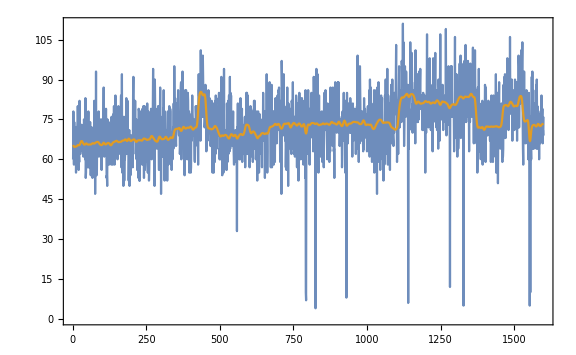
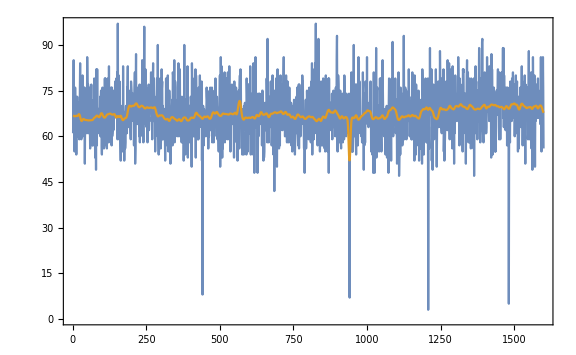
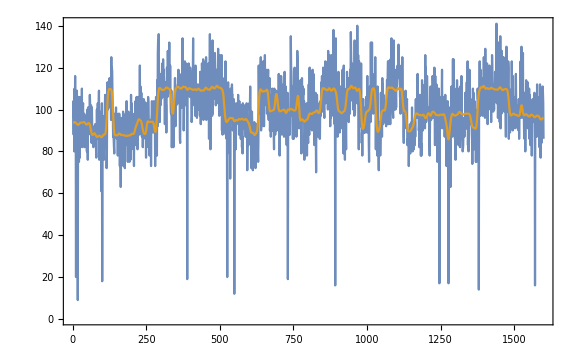
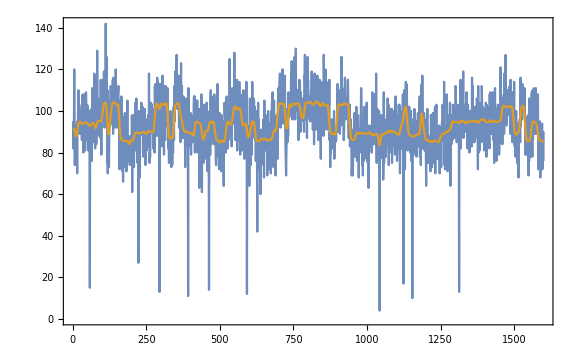
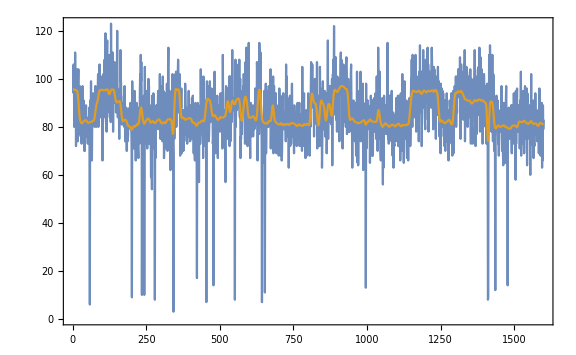
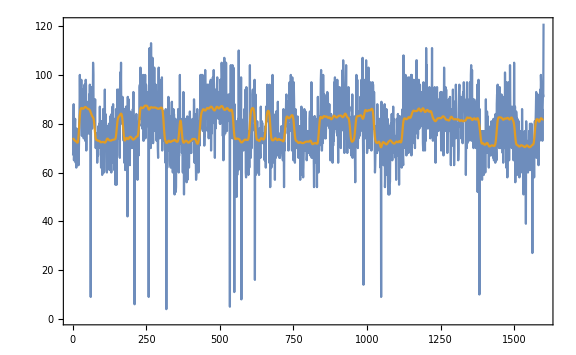
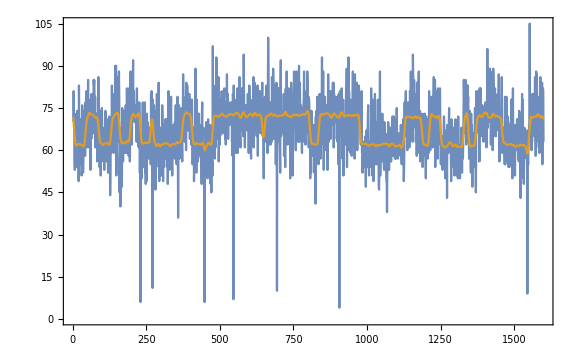
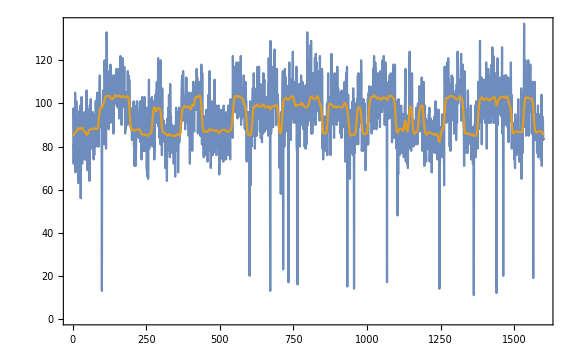

```mathematica
plotsFiltered=ListLinePlot[
{datasets[[#,;;;;75]],res1[[#,;;;;75]]},
PlotRange->Full,
PlotStyle->{{
Opacity[0.9]},
{Opacity[1.0]}
}
]&/@Range[Length[datasets]]
```

#### Remove Background/Drifts

```mathematica
InterpolateTo[dataset_,length_]:=With[
{interpolatedDataset=ListInterpolation[dataset,{0,length+1}]},
interpolatedDataset[Range[length]]
];
```

```mathematica
BackgroundRemove[dataset_,cutoff_]:=With[{},
InterpolateTo[
LowpassFilter[
GaussianFilter[
LowpassFilter[
dataset[[;;;;IntegerPart[cutoff/10]]],
1/(1.5*cutoff)
][[;;;;IntegerPart[cutoff/4]]],
{cutoff*10,cutoff}
],
1/(1.5*cutoff)
],Length[dataset]]
];
```

```mathematica
AbsoluteTiming[
res2=BackgroundRemove[#,100]&/@res1;
res21=res1-res2;
]
```

{3.38706,Null}

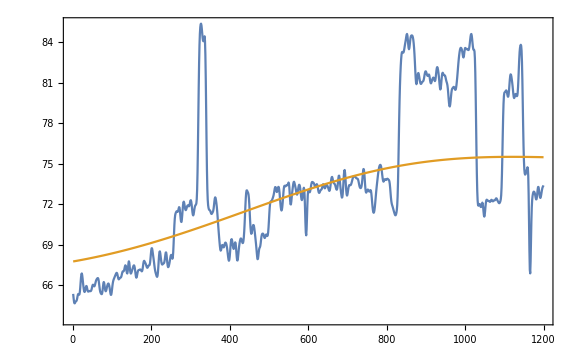
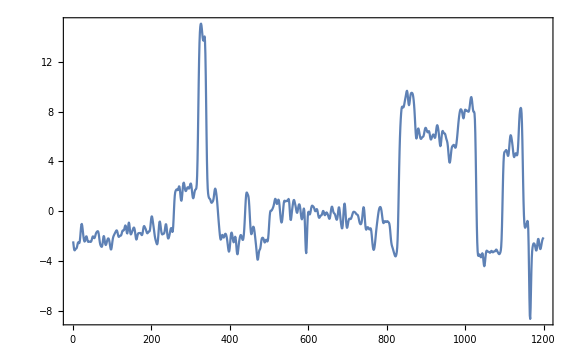
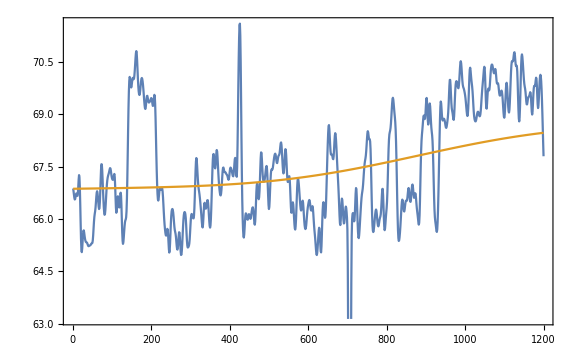
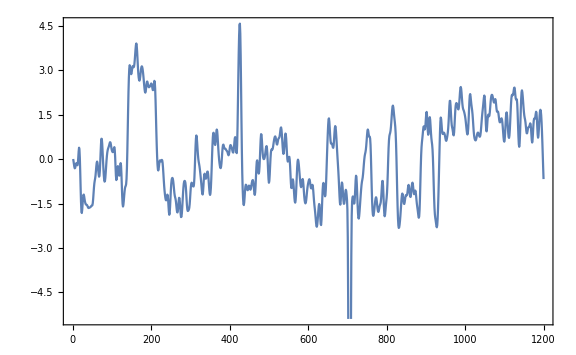
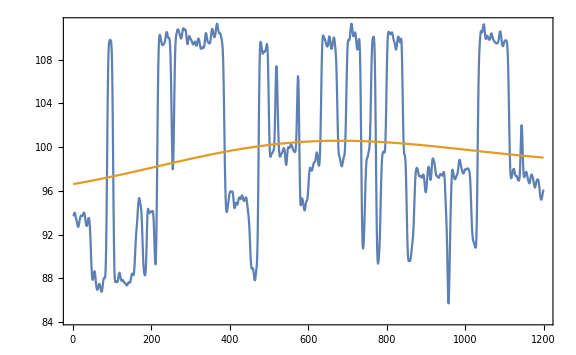
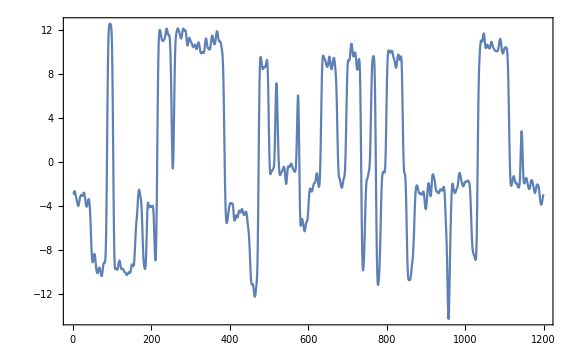
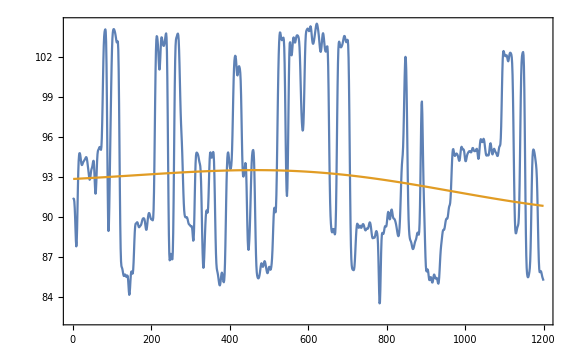
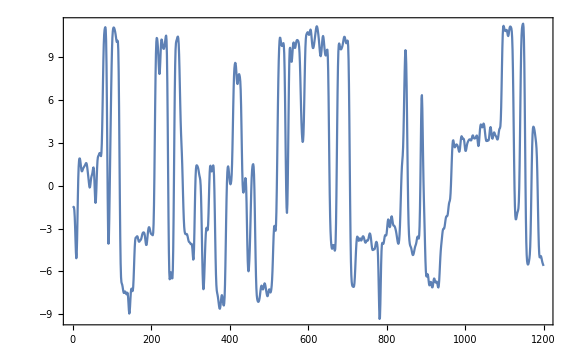

```mathematica
plotsBackgroundRemoved={
ListLinePlot[{res1[[#,;;;;100]],res2[[#,;;;;100]]},PlotRange->Automatic],
ListLinePlot[res1[[#,;;;;100]]-res2[[#,;;;;100]],PlotRange->Automatic]
}&/@Range[Length[datasets]]
```

#### Discriminate Dataset Distributions

```mathematica
DiscriminateDataset[dataset_]:=With[
{thresholdValue=FindThreshold[dataset]},
HeavisideTheta[dataset-thresholdValue]
];
```

```mathematica
AbsoluteTiming[
res3=ParallelMap[DiscriminateDataset[#]&,res21];
res4=N[Mean/@res3];
]
```

{0.447808,Null}

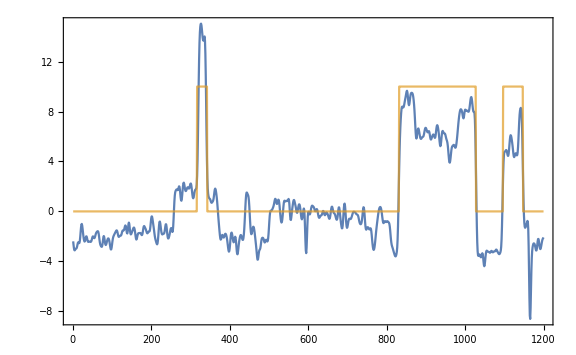
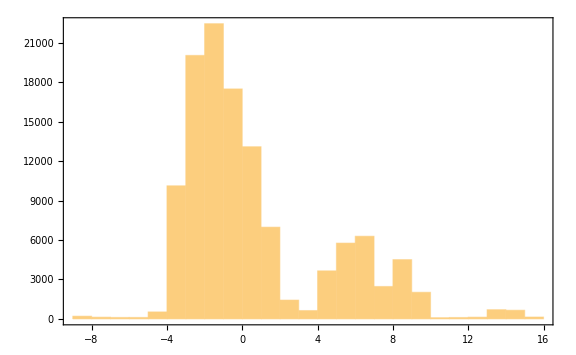
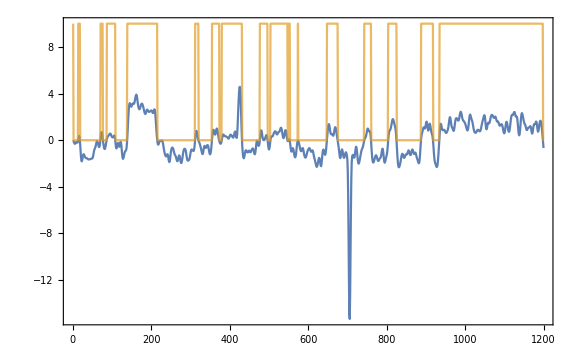
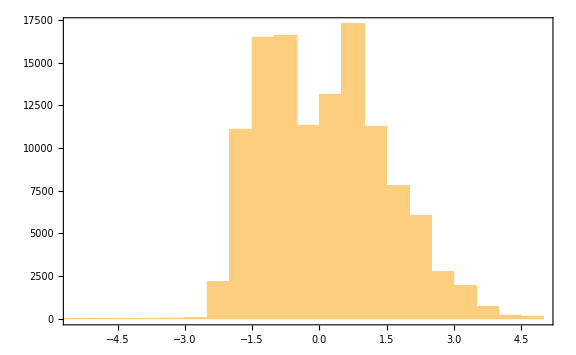
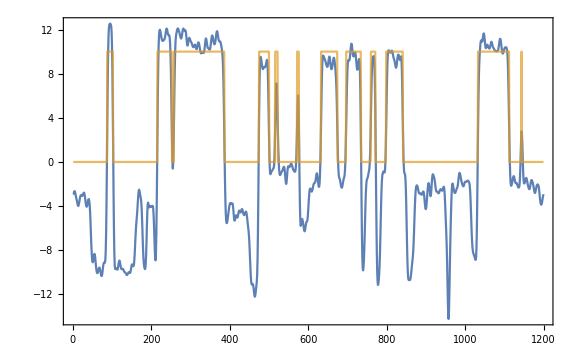
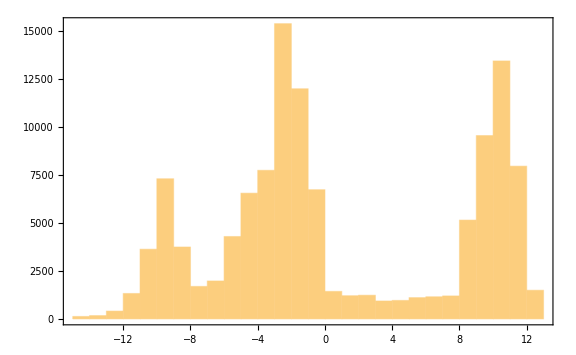
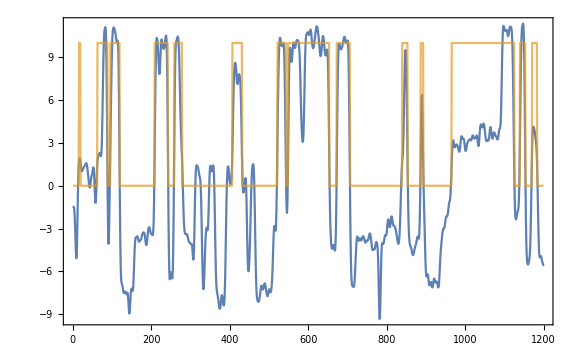
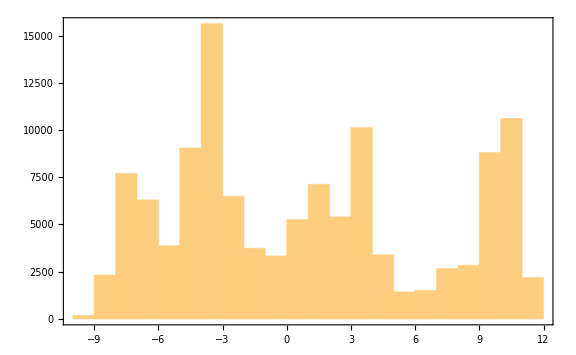
{{{2.82037,0.22751},-Graphics-,-Graphics-},{{-0.0214121,0.514263},-Graphics-,-Graphics-},{{2.59882,0.362511},-Graphics-,-Graphics-},{{1.62656,0.417837},-Graphics-,-Graphics-},{{1.30185,0.337394},-Graphics-,-Graphics-},{{-0.487544,0.543946},-Graphics-,-Graphics-},{{-0.98383,0.542971},-Graphics-,-Graphics-},{{0.765154,0.550671},-Graphics-,-Graphics-},{{1.29099,0.366928},-Graphics-,-Graphics-},{{-0.71581,0.575088},-Graphics-,-Graphics-}}

```mathematica
plotsDiscriminated={
{FindThreshold[res21[[#]]],res4[[#]]},
ListLinePlot[
{res21[[#,;;;;100]],res3[[#,;;;;100]]*10},
PlotRange->Automatic,
PlotStyle->{{Opacity[1.0]},{Opacity[0.7]}}
],
Histogram[res21[[#1]]]
}&/@Range[Length[datasets]]
```

#### Create Summary Figure

```mathematica
th12Powers
```

{38.7475,34.9997,50.0031,46.2492,42.5014,38.7475,34.9997,50.0031,46.2492,42.5014}

```mathematica
res4
```

{0.22751,0.514263,0.362511,0.417837,0.337394,0.543946,0.542971,0.550671,0.366928,0.575088}

```mathematica
resFinal=GroupBy[Transpose[{th12Powers,res4}],First->Last,Mean];
resFinal=KeySort[resFinal];
```

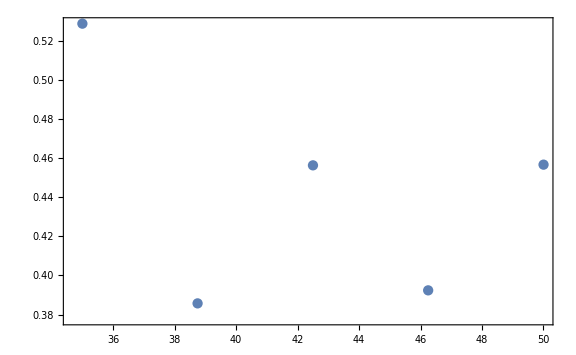

```mathematica
ListPlot[resFinal]
```

#### thkim resume

```mathematica
(*get correct key-value for dataset*)
datasetKey=First@Cases[Keys[dataFile],_?(StringContainsQ[#,"/datasets/reaction_monitoring"]&)];
datasetHolder=dataFile[datasetKey];
```

```mathematica
(*number of separate datasets*)
numDatasets=Dimensions[datasetHolder][[2]];
```

```mathematica
(*make datasets easier to work with; reduce according *)
datasetHolder=Transpose[datasetHolder[[;;;;reductionFactor]]];
```

### Direct Import Dataset

```mathematica
(*datasetHolder={dataset[[;;27356,2]]};
numDatasets=1;*)
```

## Processing

### Rates & Related

```mathematica
(*get timing data from dataset*)
sampleRate=dataFile["/datasets/sample_rate_hz"]*1/reductionFactor;
sampleTime=1/sampleRate;
```

```mathematica
numPoints=Max[Dimensions[datasetHolder]];
```

```mathematica
timeArr=Range[numPoints]*sampleTime;
```

### Frequency Array

```mathematica
(*get double-sided frequency array*)
freqArrDouble=Range[0,sampleRate,sampleRate/(numPoints-1)];
```

```mathematica
(*get single-sided frequency array*)
freqArrSingle=GetSingleSidedX[freqArrDouble];
```

### Data

```mathematica
(*mean*)
{datasetMean,datasetStdev}={Mean/@#,StandardDeviation/@#}&[datasetHolder];
```

```mathematica
(*oscillation only*)
datasetOscillation=datasetHolder-datasetMean;
```

```mathematica
(*create zoomed-in datasets*)
startPoint=100;stopPoint=200;
shortenedDatasets=datasetOscillation[[;;,startPoint;;stopPoint]];
```

```mathematica
(*process statistics for shortened datasets*)
{shortenedDatasetsMean,shortenedDatasetsStdev}={Mean/@#,StandardDeviation/@#}&[shortenedDatasets];
```

## Time-Series

## Process

### Time-Series Data

```mathematica
(*create titles with mean and rms*)
timeDomainTitlesFull=names[[#]]<>": "<>ToString[NumberForm[datasetMean[[#]]*1000,{∞,3}]]<>" ± "<>ToString[NumberForm[datasetStdev[[#]]*1000,{∞,3}]]<>"mV"&/@Range[Length[names]];
timeDomainTitlesZoom=names[[#]]<>" (Zoomed In): "<>ToString[NumberForm[shortenedDatasetsMean[[#]]*1000,{∞,4}]]<>" ± "<>ToString[NumberForm[shortenedDatasetsStdev[[#]]*1000,{∞,4}]]<>"mV"&/@Range[Length[names]];
```

```mathematica
(*create full plots*)
timeFullPlots=ListLinePlot[datasetOscillation[[#,2;;]],
PlotRange->Full,
DataRange->{0,numPoints*sampleTime},
FrameLabel->{
 {Style["Voltage (V)",{Black,Directive[15]}],None},
{Style["Time (s)",{Black,Directive[15]}],Style[timeDomainTitlesFull[[#]],{Black,Directive[15]}]}
}
]&/@Range[numDatasets];
```

```mathematica
(*create zoomed-in plots*)
timeZoomPlots=ListLinePlot[shortenedDatasets[[#]],
PlotRange->Full,
DataRange->{startPoint*sampleTime,stopPoint*sampleTime},
FrameLabel->{
 {Style["Voltage (V)",{Black,Directive[15]}],None},
{Style["Time (s)",{Black,Directive[15]}],Style[timeDomainTitlesZoom[[#]],{Black,Directive[15]}]}
}
]&/@Range[numDatasets];
```

### Filtered Data

#### Process Data

```mathematica
(*number of samples to try and filter line noise*)
(*filterSampleNum=8*Ceiling[sampleRate/30];*)
```

```mathematica
(*create line-noise filtered datasets*)
AbsoluteTiming[
(*filteredDataset=ParallelMap[MeanFilter[#,filterSampleNum]&,datasetOscillation];*)
filteredDataset=ParallelMap[LowpassFilter[#,30,SampleRate->sampleRate]&,datasetOscillation];
filteredShortenedDatasets=filteredDataset[[;;,startPoint;;stopPoint]];
]
```

{0.121282,Null}

```mathematica
(*calculate filtered mean*)
filteredDatasetMean=Mean/@filteredDataset;
filteredShortenedDatasetsMean=Mean/@filteredShortenedDatasets;
```

```mathematica
(*filtered shortened dataset rms*)
filteredDatasetStdev=StandardDeviation/@filteredDataset;
filteredShortenedDatasetsStdev=StandardDeviation/@filteredShortenedDatasets;
```

#### Format Plots

```mathematica
(*create titles with mean and rms*)
filteredTimeDomainTitlesFull=names[[#]]<>": "<>ToString[NumberForm[Round[filteredDatasetMean[[#]]*1000,1*^-5],{∞,3}]]<>" ± "<>ToString[NumberForm[filteredDatasetStdev[[#]]*1000,{∞,3}]]<>"mV"&/@Range[Length[names]];
filteredTimeDomainTitlesZoom=names[[#]]<>" (Zoomed In): "<>ToString[NumberForm[Round[filteredShortenedDatasetsMean[[#]]*1000,1*^-5],{∞,4}]]<>" ± "<>ToString[NumberForm[filteredShortenedDatasetsStdev[[#]]*1000,{∞,4}]]<>"mV"&/@Range[Length[names]];
```

```mathematica
(*create full plots*)
filteredTimeFullPlots=ListLinePlot[
filteredDataset[[#,2;;]],
PlotRange->Full,
DataRange->{0,numPoints*sampleTime},
FrameLabel->{
 {Style["Voltage (V)",{Black,Directive[15]}],None},
{Style["Time (s)",{Black,Directive[15]}],Style[filteredTimeDomainTitlesFull[[#]],{Black,Directive[15]}]}
}
]&/@Range[numDatasets];
```

```mathematica
(*create zoomed-in plots*)
filteredTimeZoomPlots=ListLinePlot[filteredShortenedDatasets[[#]],
PlotRange->Full,
DataRange->{startPoint*sampleTime,stopPoint*sampleTime},
FrameLabel->{
 {Style["Voltage (V)",{Black,Directive[15]}],None},
{Style["Time (s)",{Black,Directive[15]}],Style[filteredTimeDomainTitlesZoom[[#]],{Black,Directive[15]}]}
}
]&/@Range[numDatasets];
```

## Export Plots

```mathematica
(*export full plots*)
fullPlotNames=#<>"TimeFull"&/@names;
ExportPlots[fullPlotNames,timeFullPlots];
```

```mathematica
(*export zoomed plots*)
zoomPlotNames=#<>"TimeZoom"&/@names;
ExportPlots[zoomPlotNames,timeZoomPlots];
```

```mathematica
(*export filtered full plots*)
filteredFullPlotNames=#<>"TimeFull_filtered"&/@names;
ExportPlots[filteredFullPlotNames,filteredTimeFullPlots];
```

```mathematica
(*export filtered zoomed plots*)
filteredZoomPlotNames=#<>"TimeZoom_filtered"&/@names;
ExportPlots[filteredZoomPlotNames,filteredTimeZoomPlots];
```

$Aborted

$Aborted